```mathematica
UnitTest[ description_, val_, expr_ ] := 
	If [val == expr, "ok", StringJoin[ "ERROR: GOT UNEXPECTED VALUE ", ToString[expr], " INSTEAD OF ", ToString[val]]]
```

{{2,150},{3,188},{4,246},{5,282},{6,362},{7,436},{8,540},{9,632},{10,750},{11,870},{12,990},{13,1115},{14,1270},{15,1440},{16,1608},{17,1780},{18,1950}}

{{150,2},{188,3},{246,4},{282,5},{362,6},{436,7},{540,8},{632,9},{750,10},{870,11},{990,12},{1115,13},{1270,14},{1440,15},{1608,16},{1780,17},{1950,18}}

93.8676+16.2393 x+4.86365 x^2

100+15 x+5 x^2

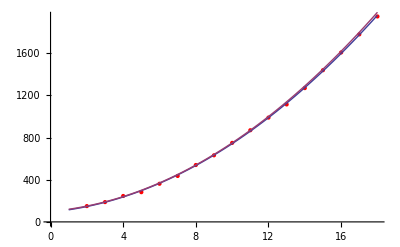

```mathematica
(* Curve fitting to find exp growth as a function of time *)
data = { (* level,game-time (seconds) *)
{2,150},
{3,188},
{4,246},
{5,282},
{6,362},
{7,436},
{8,540},
{9,632},
{10,750},
{11,870},
{12,990},
{13,1115},
{14,1270},
{15,1440},
{16,1608},
{17,1780},
{18,1950}
}
data2 = {#[[2]],#[[1]]}& /@ data
parabola = Fit[data, {1,x,x^2}, x]
para2 = 100+15x+5 x^2
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola,para2},{x,1,18}]]
(*
parabola2 = Fit[data2, {1,x, x^2}, x]
parabola3 =0.72 +0.0145 x-3.0*^-6 x^2
Show[ListPlot[data2,PlotStyle->Red],Plot[{parabola3,parabola3},{x,150,2000}]]

levelAt[t_/; t > 100] := 1/10 (-15+Sqrt[5] Sqrt[-355+4 t])
levelAt[t_]:=1
*)

timeAt[lv_] := 100+15lv+5 lv^2
timeAt[1] := 0
```

LV | Gold
1 | 475
2 | 967.
3 | 1163.
4 | 1526.
5 | 1880.
6 | 2284.
7 | 2834.
8 | 3406.
9 | 4004.
10 | 4753.
11 | 5559.
12 | 6366.
13 | 7366.
14 | 8365.
15 | 9430.
16 | 10672.
17 | 11953.
18 | 13273.

840.777+38.4742 x^2

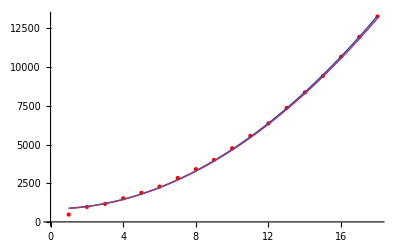

```mathematica
(* Exact gold generation over time and approximate formula *)
wavesPerSecond = 1/30;
siege2Wave = (35*60) wavesPerSecond;
upgradeCycle = 180; (*seconds*)
firstWaveAt = 90; (*seconds*)

cycle[t_] := Floor[t / upgradeCycle]

minionCaster[t_] := 16.5 + 0.5 cycle[t]
minionMelee[t_] := 22.5 + 0.5 cycle[t]
minionSiege[t_] := 27 + 1 cycle[t]

waveGold[t_,w_Integer/; w ≤ 0] := 0
waveGold[t_,w_Integer] := waveGold[t-30,w-1] + 3 minionCaster[t] + 3 minionMelee[t] + Boole@(Mod[w,If[w ≥ siege2Wave,2,3]]==0)minionSiege[t]

minionGoldAt[t_] := waveGold[t,Floor[(t-60) wavesPerSecond]]
(* TODO: make sure this is right *)
Clear[passiveGoldAt]
passiveGoldAt[t_/; t < firstWaveAt] := 0
passiveGoldAt[t_] := ((t-firstWaveAt)/10)*19 (*summoner's rift*)
exactGoldAtTime[t_] := minionGoldAt[t] + passiveGoldAt[t] + 475

data = {#,exactGoldAtTime[timeAt[#]]}& /@ Range[1,18];
Join[{{"LV","Gold"}},data] // TableForm
parabola = Fit[data, {1, x^2}, x]
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola,840+38 x^2},{x,1,18}]]

goldAtLV[lv_]:= 840 + 38 lv^2
```

```mathematica
armor[ppen_] := (100/(100+(xArmor*ppen)))


(*
#define AS_OFFSET         (-0.04)
perlvAS := 0.0322f
baseAS := (0.625/(1+AS_OFFSET))
	float level = (float)(LV - 1);
	float bonus = PERCENT(GEAR);

	return min(2.5f, AS_BASE * (1.0f + (AS_LVPER*level) + bonus));
*)
             (*1 2 3 4 5 6 7 8 9 10 11 12 13 14 15 16 17 18 *)
upgradepath = {3,1,2,2,2,4,2,2,3,3, 4, 3, 3, 1, 1, 4, 1, 1 };
abilityRank = Module[{r={0,0,0,0},n=#}, 
	While[n>0, r⟦upgradepath⟦n⟧⟧++; n--]; r]&/@Range[1,Length[upgradepath]
	];
sheenproc[] := {xBaseAttack*xSpellBlade, 2, 1}
tickrate = 0.5;

hitenStyle = {
	{15 xAttackSpeed tickrate, 15, 6 1/tickrate},
	{30 xAttackSpeed tickrate, 15, 6 1/tickrate},
	{45 xAttackSpeed tickrate, 15, 6 1/tickrate},
	{60 xAttackSpeed tickrate, 15, 6 1/tickrate},
	{75 xAttackSpeed tickrate, 15, 6 1/tickrate}
	};
bladeSurge[mitigation_]:= Module[{a={
	{20,14,1}, 
	{50,12,1},
	{80,10,1},
	{110,8,1},
	{140,6,1}}},
	a⟦All,1⟧ = mitigation*(#+xAttack)&/@a⟦All,1⟧; a]

equilibriumStrike[mitigation_] := Module[{a={
	{80,8,1},
	{130,8,1},
	{180,8,1},
	{230,8,1},
	{280,8,1}
	}},
	a⟦All,1⟧ = mitigation * (#+(xAbilityPower/2))&/@a⟦All,1⟧; a]

transcendentBlades[mitigation_] := Module[{a={
	{80,70,4},
	{120,60,4},
	{160,50,4}
	}},
	a⟦All,1⟧ = mitigation * (#+(xAbilityPower/2)+(xAttack*6/10))&/@a⟦All,1⟧; a]

Clear[abilities,dps]
priority = {2,4,3,1}
abilities[level_Integer/;level < 1,_] := {}
abilities[level_Integer, mitigation_] := Module[{xs,ys},
	xs={bladeSurge[mitigation], hitenStyle, equilibriumStrike[mitigation], transcendentBlades[mitigation]};
	ys=MapIndexed[If[#1>0,First@xs⟦#2,#1⟧, Undefined]&, abilityRank⟦level⟧];
	Select[ys⟦priority⟧, !MatchQ[#,Undefined]&]
]

autoAttackDmg[resist_] := resist * xAttack * xCriticalStrike

applyDoT[{{dmg_,cooldown_,duration_},0}] := 0
applyDoT[{{dmg_,cooldown_,duration_},timer_}] := If[cooldown-timer < duration, dmg, 0]

useAbility[as_,cs_,trickrate_]:= Module[{cs2,pos,i,dmg},
	cs2=Max[0,#-trickrate]&/@cs;
	pos=Position[cs2, 0]; 
	If [Length[pos] ≠ 0, i=First@First@pos; cs2⟦i⟧ = as⟦i⟧⟦2⟧];
	dmg=Total[applyDoT/@Thread[{as,cs2}]];
	{cs2, dmg}
	]


simstep[{spell_, aa_, spd_, spellblade_}, {health_, cooldowns_, result_}] := Module[{cs,sdmg,aadmg,total},
		{cs,sdmg}=useAbility[spell,cooldowns,tickrate];
		If[Mod[result⟦1⟧,2] == 0, sdmg += spellblade];
		aadmg = (aa*spd)*tickrate;
		total = sdmg+aadmg;
		{health-total, cs, result + {tickrate,sdmg,aadmg,total}}
	]

siminit[level_, self_, enemy_, armorReduction_, maxduration_] := Module[{mitigation,spell},
	mitigation=armor[armorReduction] //. enemy;
	spell=abilities[level, mitigation];
	{maxduration, {spell, autoAttackDmg[mitigation], xAttackSpeed, xSpellBlade * xBaseAttack} //. self, {xHealth/.enemy, ConstantArray[0,Length[spell]], {0,0,0,0}}}]

mresult[{time_,sdmg_,aadmg_,total_}] := {ElapsedTime -> time, SpellDamage -> sdmg, AutoAttackDamage -> aadmg, TotalDamage -> total}

tick[{duration_/; duration ≤ 0, _, ctx2_}] := mresult[ctx2⟦3⟧]
tick[{duration_, ctx_, {health_/; health ≤ 0, _, result_}}] := mresult[result]
tick[{duration_, ctx_, {health_?NumericQ, cooldowns_, result_}}] := tick[{duration-tickrate,ctx,simstep[ctx, {health, cooldowns, result}]}]

combatSim[level_Integer/; level < 1, self_, enemy_, armorReduction_, maxduration_] := 0
combatSim[level_Integer, self_, enemy_, armorReduction_, maxduration_] := tick@siminit[level, self, enemy, armorReduction, maxduration]

abilities[9,1]
abilities[16,1]
st1 = {xBaseAttack :> 80, xAttack :> 100, xCriticalStrike :> 1, xAttackSpeed -> 1.0, xSpellBlade :> 1, xAbilityPower :> 0}
st2 = {xBaseAttack :> 80, xAttack :> 100, xCriticalStrike :> 1, xAttackSpeed -> 2.0, xSpellBlade :> 0, xAbilityPower :> 0}
combatSim[3, st1, {xHealth :> 1000, xArmor :> 10}, 1.0, 4] 
combatSim[3, st2, {xHealth :> 1000, xArmor :> 10}, 1.0, 4] 
(*{7,451.81818181818187,636.3636363636363}*)
{unused,ctx1,ctx2} = siminit[3, st1, {xHealth :> 1000, xArmor :> 10}, 1.0, Infinity] 
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
HoldForm[armor] // TeXForm
```

{2,4,3,1}

{{37.5 xAttackSpeed,15,12.},{80+xAbilityPower/2+(3 xAttack)/5,70,4},{130+xAbilityPower/2,8,1},{20+xAttack,14,1}}

{{37.5 xAttackSpeed,15,12.},{160+xAbilityPower/2+(3 xAttack)/5,50,4},{280+xAbilityPower/2,8,1},{80+xAttack,10,1}}

{xBaseAttack:>80,xAttack:>100,xCriticalStrike:>1,xAttackSpeed→1.,xSpellBlade:>1,xAbilityPower:>0}

{xBaseAttack:>80,xAttack:>100,xCriticalStrike:>1,xAttackSpeed→2.,xSpellBlade:>0,xAbilityPower:>0}

{ElapsedTime→4.,SpellDamage→583.636,AutoAttackDamage→363.636,TotalDamage→947.273}

{ElapsedTime→3.5,SpellDamage→468.636,AutoAttackDamage→636.364,TotalDamage→1105.}

{∞,{{{7.5,15,12.},{72.7273,8,1},{109.091,14,1}},90.9091,1.,80},{1000,{0,0,0},{0,0,0,0}}}

{867.045,{15,0,0},{0.5,87.5,45.4545,132.955}}

{741.364,{14.5,8,0},{1.,167.727,90.9091,258.636}}

{506.591,{14.,7.5,14},{1.5,357.045,136.364,493.409}}

{344.545,{13.5,7.,13.5},{2.,473.636,181.818,655.455}}

{211.591,{13.,6.5,13.},{2.5,561.136,227.273,788.409}}

{158.636,{12.5,6.,12.5},{3.,568.636,272.727,841.364}}

\text{armor}

```mathematica
gold := goldAtLV[lv]

costAttack = 36;
costHealth = 2.64;
costArmor = 20;
costAbilityPower = 21.75;
costCriticalChance = 50*100;
costAttackSpeed = 33.33*100;
attackSpeedBase = 0.625;
(*
championIrelia[HealthBase]       = 456;
championIrelia[HealthLv]         = 90;
championIrelia[AttackBase]       = 56;
championIrelia[AttackLv]         = 3.3;
championIrelia[ArmorBase]        = 15;
championIrelia[ArmorLv]          = 3.75;
championIrelia[AttackSpeedBase]  = 0.625;
championIrelia[AttackSpeedDelay] = −0.06;
championIrelia[AttackSpeedLv]    = 0.0322;*)
<< "D:\GitRoot\llio\src\league\database\generator\db_champion.m"

stats[lv_, c_, spellblade_] := With[{
	baseHP = c[HealthBase] + c[HealthLv](lv-1),
	baseAD = c[AttackBase] + c[AttackLv](lv-1),
	baseArmor = c[ArmorBase] + c[ArmorLv](lv-1),
	crit = With[{ξ=gCriticalChance/costCriticalChance}, 1 + (1 *Min[1,ξ])],
	aspd = With[{ξ=gAttackSpeed/costAttackSpeed}, Min[2+1/2, (attackSpeedBase/(1+c[AttackSpeedDelay])) * (1 + (c[AttackSpeedLv]*(lv-1)) + ξ)]]
	},
	
	{xBaseAttack       -> baseAD, 
	 xAttack           -> baseAD + (gAttack/costAttack), 
	 xHealth           -> baseHP +(gHealth/costHealth), 
	 xArmor            -> baseArmor + (gArmor/costArmor),
	 xAbilityPower     -> (gAbilityPower/costAbilityPower),
     xCriticalStrike   -> crit, 
	 xAttackSpeed      -> aspd,
     xSpellBlade       -> spellblade}
]

statsym = {gAttack, gCriticalChance, gAttackSpeed, gHealth, gArmor, gAbilityPower};
gdistro[xs__] := Map[# -> gold 1/Length[{xs}]&, {xs}] ~Join~ gdistro[]
gdistro[] := # -> 0& /@ statsym
evendistro = gdistro@@statsym;

stats[18, championIrelia, 0] /. gdistro[]
"===="

Clear[metric]
Options[metric] = {
    ArmorScale -> 1,
    SpellBlade -> 0,
	TimeLimit -> Infinity
}

metric[lv_/;lv > 0, champ_, distro_, opts:OptionsPattern[]] := With[{
	me = stats[Floor[lv], champ, OptionValue[SpellBlade]] //. distro, 
	him = stats[Floor[lv], champ, 0] //. gdistro[gAttackSpeed,gHealth,gAttack,gArmor,gCriticalChance] },

	{combatSim[Floor[lv], me, him, OptionValue[ArmorScale], OptionValue[TimeLimit]],
	 combatSim[lv, him, me, OptionValue[ArmorScale], OptionValue[TimeLimit]]}
]

Block[{lv=5}, metric[lv, championIrelia, gdistro[gAttackSpeed,gHealth,gAttack]]]
Block[{lv=5}, metric[lv, championIrelia, gdistro[gAttack]]]
```

{xBaseAttack→112.1,xAttack→112.1,xHealth→1986.,xArmor→78.75,xAbilityPower→0.,xCriticalStrike→1,xAttackSpeed→1.0266,xSpellBlade→0}

====

{ArmorScale→1,SpellBlade→0,TimeLimit→∞}

{{ElapsedTime→8.,SpellDamage→564.066,AutoAttackDamage→403.192,TotalDamage→967.257},{ElapsedTime→8.5,SpellDamage→589.799,AutoAttackDamage→455.504,TotalDamage→1045.3}}

{{ElapsedTime→7.,SpellDamage→532.291,AutoAttackDamage→422.138,TotalDamage→954.429},{ElapsedTime→6.,SpellDamage→497.389,AutoAttackDamage→321.532,TotalDamage→818.922}}

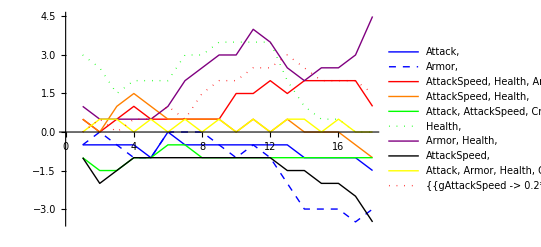

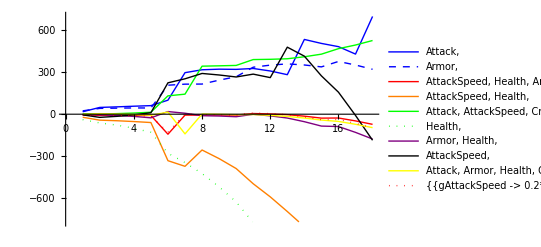

13152

```mathematica
iTrinity     = {3, {10,50,5,1,0,0.10}};
iZeal        = {375,{0,0,0,0,0.02,0.08}};
iDagger      = {400,{0,0,0,0,0,0.12}};
iBrawlGlove  = {400,{0,0,0,0,0.08,0}};
iSheen       = {1200,{0,0,25,1,0,0}};
iPhage       = {490,{10,20,0,0,0,0}};
iRubyCrystal = {475,{0,180,0,0,0,0}};
iLongSword   = {360,{10,0,0,0,0,0}};
buildPath1 = {iRubyCrystal,iSheen,iLongSword,iDagger,iBrawlGlove,iZeal,iPhage,iTrinity};
buildPath2 = {iRubyCrystal,iLongSword,iDagger,iBrawlGlove,iZeal,iSheen,iPhage,iTrinity};
buildPath3 = {iRubyCrystal,iLongSword,iSheen,iDagger,iBrawlGlove,iZeal,iPhage,iTrinity};

trinityforce[gold_Integer, buildpath_] := With[
	{x=Reverse[Select[FoldList[#1+#2&, {0,{0,0,0,0,0,0}}, buildpath], #⟦1⟧ < gold&]]⟦1,2⟧,
	 extra = Max[0,(gold-3703)/3]
	},
	{{gAttack -> (x⟦1⟧*costAttack), 
	  gHealth -> (x⟦2⟧*costHealth) + extra, 
	  gAbilityPower -> x⟦3⟧*costAbilityPower, 
	  gCriticalChance -> x⟦5⟧*costCriticalChance,
	  gAttackSpeed -> (x⟦6⟧*costAttackSpeed) + extra,
	  gArmor -> extra
	}, x⟦4⟧}
]


dataset = { 
	(*{gAttack},{gAttackSpeed}, {gCriticalChance}, {gHealth}, {gArmor}*)

	  {gAttack},
	  {gArmor},
	  {gAttackSpeed, gHealth, gArmor},
	  {gAttackSpeed, gHealth},
	  {gAttack, gAttackSpeed, gCriticalChance},
	  {gHealth},
	  {gArmor, gHealth},
	  {gAttackSpeed},
	  {gAttack, gArmor, gHealth, gCriticalChance} 
	};

dataset2 = {
	{{gAttackSpeed -> gold*0.20, gHealth -> gold*0.40, gArmor -> gold*0.40}, 0} (*, 
	trinityforce[gold, buildPath1],
	trinityforce[gold, buildPath2],
	trinityforce[gold, buildPath3] *)};

colors = {Blue,
		  Directive[Dashed,Blue,Thick],
		  Red,
		  Directive[Orange],
		  Green, 
	      Directive[Dotted,Green,Thick],
		  Directive[Purple],
		  Black,
		  Directive[Yellow],
		  Directive[Dotted,Red,Thick],
		  Directive[Dotted,Purple,Thick]
};
label[x_] := StringDrop[ToString[x],1]
label[xs_List] := StringJoin[({label[#], ", "}&)/@xs]

rating[Duel][{out_,in_}] := (ElapsedTime/.in) - (ElapsedTime/.out)
rating[Poke][{out_,in_}] := (TotalDamage/.out) - (TotalDamage/.in)

measure[r_][level_] := Block[{lv=level},(rating[r]@metric[lv, championIrelia, #⟦1⟧, ArmorScale -> 0.64, SpellBlade -> #⟦2⟧, TimeLimit -> If[r == Poke, 4, Infinity]]&)/@Join[
	{gdistro@@#,0}&/@dataset, 
	{#⟦1⟧~Join~gdistro[], #⟦2⟧}&/@dataset2]];
(*
Plot[measure[lv], {lv,0,18}, PlotLegends->label/@dataset, PlotStyle-> colors]
*)

sample[f_] := Transpose[Thread[{#,f[#]}]&/@Range[1, 18]];
legend[] := Join[label/@dataset, ToString[#,FormatType -> InputForm]&/@dataset2]

ListLinePlot[sample[measure[Duel]], PlotLegends -> legend[], PlotStyle-> colors]
ListLinePlot[sample[measure[Poke]], PlotLegends -> legend[], PlotStyle-> colors]
goldAtLV[18]
```

```mathematica
NMaximize[{Block[{lv=#},metric[lv, championIrelia, 0, 0.94]], {Total[statsym] == 1}, Thread[statsym ≥ -0.001], Thread[statsym ≤ 1]}, statsym, AccuracyGoal -> 2, PrecisionGoal -> 2]& /@ {1,6,11,16,18}
```

{{4.27499,{gAttack→0.0642178,gCriticalChance→0.0113799,gAttackSpeed→0.150488,gHealth→0.672991,gArmor→0.0340201,gAbilityPower→0.066903}},{5.30909,{gAttack→0.0752857,gCriticalChance→0.0127408,gAttackSpeed→0.0358714,gHealth→0.771508,gArmor→0.105642,gAbilityPower→-0.00104812}},{0.906504,{gAttack→-0.000999999,gCriticalChance→-0.000999999,gAttackSpeed→0.645598,gHealth→0.358402,gArmor→-0.000999999,gAbilityPower→-0.000999989}},{2.31331,{gAttack→-0.001,gCriticalChance→-0.001,gAttackSpeed→0.542716,gHealth→0.461284,gArmor→-0.001,gAbilityPower→-0.000999987}},{2.98479,{gAttack→0.00187079,gCriticalChance→0.00645131,gAttackSpeed→0.603907,gHealth→0.165197,gArmor→0.213893,gAbilityPower→0.00868097}}}

```mathematica
trinityforce[goldAtLV[1]]
{goldAtLV[1],goldAtLV[1]/2/costHealth,goldAtLV[1]*1.0/2/costAttack}
trinityforce[goldAtLV[4]]
trinityforce[goldAtLV[6]]
trinityforce[goldAtLV[8]]
trinityforce[goldAtLV[9]]
```

{gAttack→0,gHealth→0.,gAbilityPower→0.,xSpellBlade→0,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{878,166.288,12.1944}

{gAttack→0,gHealth→0.,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→360,gHealth→475.2,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→720,gHealth→528.,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→399.96,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→1080,gHealth→660.,gAbilityPower→652.5,xSpellBlade→2,gCriticalChance→500.,gAttackSpeed→999.9,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

7500

***

(50+ad/36) (1+crit/5000)

{1/36 (1+crit/5000),(50+ad/36)/5000}

0.0503813

0.0523639

0.0425426

0.0660153

==

0.0318368

0.034801

1/36 (1+crit/5000) Dt[ad]+((50+ad/36) Dt[crit])/5000

0

--

(50+ad/36)/5000+1/36 (1+crit/5000)

|||

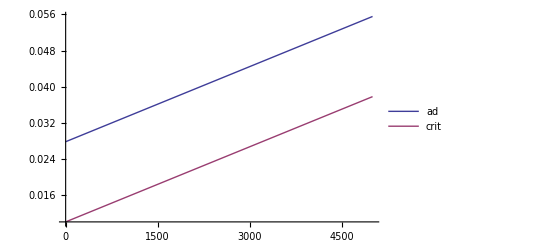

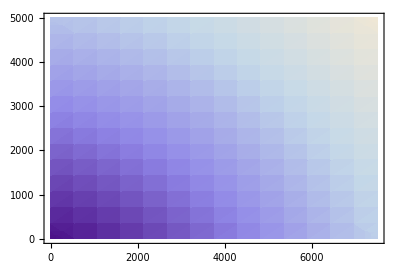

ad

crit

False

```mathematica
ClearAll[ad,crit,dps2]
range = 7500


dps2 := (50+(ad/36)) * (1 + (crit/5000))
"***"

(*
{min, {steps}} = Reap[NMaximize[{dps2, constraints}, {{ad, 0, range}, {crit, 0, range}}, 
    StepMonitor :> Sow[{ad, crit}], Method -> "DifferentialEvolution"]]
*)
dps2
grad = Grad[dps2, {ad, crit}]
f := Sqrt[grad.grad]
f /. {ad -> 5000.0, crit -> 1000.0}
f /. {ad -> 1000.0, crit -> 4000.0}
f /. {ad -> 4000.0, crit -> 0.0}
f /. {ad -> 6400.0, crit -> 3600.0} 
"=="

f /. {ad -> 1000.0, crit -> 0.0}
f /. {ad -> 0000.0, crit -> 1000.0}
g = Dt[dps2] 
g /. {ad -> 2000, crit -> 1000}
"--"
z = grad[[1]] + grad[[2]]
"|||"
Plot[{grad[[1]] /. {crit -> x}, grad[[2]] /. {ad -> x}}, {x,0,5000}, PlotLegends->{ad,crit}]
Block[{ad,crit},DensityPlot[f, {ad, 0, range}, {crit, 0, 5000}, AspectRatio -> Automatic]]
ad
crit
hessian2 = D[dps2,{{ad,crit},2}] // MatrixForm;
HermitianQ[m_List?MatrixQ] := (m === Conjugate@Transpose@m)

Eigenvalues[hessian2];
Reduce[grad[[1]] ≤  0 && crit ≥ 0 && crit ≤ 5000, {crit}] && Reduce[grad[[2]] ≤  0 && ad ≥ 0 && crit ≤ 5000, {ad,crit}]
```

10-x^2-2 y^2

x^2/4

-Graphics3D-

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

-5000+√((1800+ad)^2)

-Graphics-

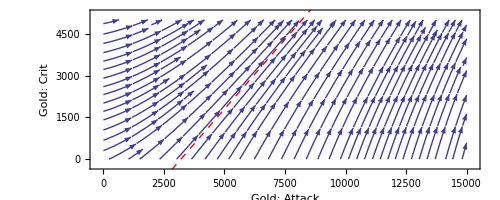

```mathematica
zxy = 10 - x^2 - 2y^2
gradAscent[f_, vars_, const_] := Module[{grad,slope,equation,x},
	grad  = Grad[f,vars];
	slope = grad[[2]] / grad[[1]];
	x     = vars[[1]];
	{equation} = y[x] /. DSolve[{y'[x] == (slope /. vars[[2]] -> y[x]), y[const⟦1⟧]==const⟦2⟧}, y[x], x];
	equation
]

eq1 = gradAscent[zxy, {x,y}, {2,1}]

Show[ParametricPlot3D[{x,y,zxy} /. y -> eq1, {x, 2, 0}, AxesLabel->{x,y,"z"}, PlotStyle -> Directive[Dashed,Red,Thick], Boxed -> True, BoxStyle -> Directive[Dotted]],
Plot3D[zxy, {x,2,0}, {y,2,0}, AxesLabel->{x,y,"z"}, PlotStyle -> Directive[Pink, Specularity[White, 50], Opacity[0.8]], ExclusionsStyle -> {None, Red}, ClippingStyle -> None, Mesh -> None, Boxed -> False]
]

eq2 = gradAscent[dps2, {ad,crit}, {6600,3400}]
dpsAscent = Plot[eq2, {ad,0,15000},  PlotStyle -> Directive[Dashed,Red,Thick]];
Show[
ContourPlot[dps2, {ad, 0, range*2}, {crit, 0, 5000}, ColorFunction-> "ThermometerColors",  
	PlotLegends -> Automatic, AspectRatio->Automatic,
	PerformanceGoal -> "Quality", Contours -> Automatic,
	ContourLabels -> True,
	FrameLabel -> {"Gold: Attack","Gold: Crit"}, 
	Epilog -> {Green, Line[steps], Red, Point[steps]}],
	dpsAscent
]
Show[
StreamPlot[grad,  {ad, 0, range*2}, {crit, 0, 5000}, 
	StreamPoints -> Fine,
	PerformanceGoal -> "Quality",
	FrameLabel -> {"Gold: Attack","Gold: Crit"}, 
	ColorFunction-> "ThermometerColors",   
	AspectRatio -> Automatic
	],
dpsAscent]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

-5000+√((1800+ad)^2)

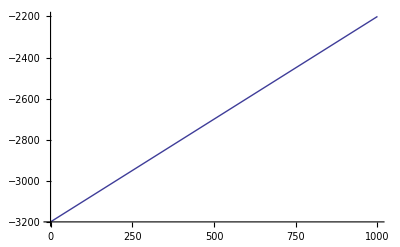

-Graphics-

{8200}

Piecewise[{{Max[0,-5000+√((1800+ad)^2)], ad≤8200}, {5000, True}}]

{(3200+x)/2}

Piecewise[{{x, x≤3200}, {(3200+x)/2, x≤13200}, {-5000+x, True}}]

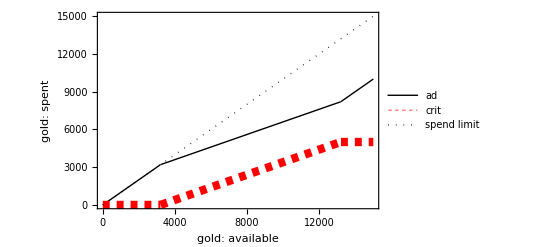

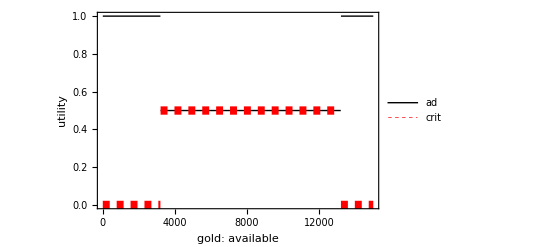

```mathematica
eq2 = gradAscent[dps2, {ad,crit}, {6600,3400}]
Plot[eq2, {ad,0,1000}]
Plot[grad[[2]]/grad[[1]], {u,0,1000}]
{critlimitAtAD} = ad /. Solve[eq2 == 5000 && ad ≥ 0, ad]
eq3 = Piecewise[{{Max[0,eq2],ad ≤ critlimitAtAD}}, 5000]
{adAmount1} = ad /. Solve[eq2 + ad == x, ad]
adAmount = Piecewise[{
	{x, x ≤ 3200},
	{adAmount1, x ≤ 5000+critlimitAtAD}}, 
	x-5000]
adValue[u_] := (adAmount) //. {x -> u, ad -> adAmount}
critValue[u_] := (eq3) //. {x -> u, ad -> adAmount}
Plot[{adValue[u], critValue[u], u}, {u,0,15000}, PlotLegends -> {ad,crit,"spend limit"}, Frame -> True, FrameLabel -> {"gold: available", "gold: spent"}, 
	PlotStyle -> {Directive[Black,Thick],
				 Directive[Dashed,Red,Thickness[0.015]],
				 Directive[Black,Dotted]}]
Plot[{adValue'[u], critValue'[u]}, {u,0,15000}, PlotLegends -> {ad,crit}, Frame -> True, FrameLabel -> {"gold: available", "utility"}, PlotStyle -> {Directive[Black,Thick],Directive[Dashed,Red,Thickness[0.015]]}]
```

```mathematica
"
```

```mathematica
(*dps2 = ad E^(-ad^2-crit^2)*)

constraints = {ad ≥ 0, crit ≥ 0, crit ≤ 5000, ad + crit ≤ 10000}

{min, {steps}} = Reap@FindMaximum[{dps2,constraints}, {{ad,0},{crit,0}}, Gradient -> grad, StepMonitor :> Sow[{ad, crit}]]
(*{min, {steps}} = Reap[NMaximize[{dps2, constraints}, {{ad, 0, range}, {crit, 0, range}}, 
    StepMonitor :> Sow[{ad, crit}], Method -> "DifferentialEvolution"]]
*)
magn[v_] := Sqrt[v.v]


dps2
dps2 /. {ad -> 5000.0, crit -> 1000}
```

{ad≥0,crit≥0,crit≤5000,ad+crit≤10000}

{{392.,{ad→6600.,crit→3400.}},{{{0.001,0.001},{0.0581094,0.622854},{29.3654,318.842},{433.982,2053.28},{5475.92,4448.95},{5788.05,4178.34},{6553.55,3425.98},{6597.5,3402.22},{6599.97,3400.03},{6600.,3400.}}}}

(50+ad/36) (1+crit/5000)

226.667

{x$21555[0]==1,y$21556[0]==1}

{x$21555'[u]==-2 x$21555[u],y$21556'[u]==-14 y$21556[u]}

{{Function[{u},ⅇ^(-2 u)],Function[{u},ⅇ^(-14 u)]}}

{ad$21564[10000]==6600,crit$21565[10000]==3400}

{ad$21564'[u]==1/36 (1+crit$21565[u]/5000),crit$21565'[u]==(50+ad$21564[u]/36)/5000}

{{Function[{u},-(600 (3 ⅇ^(1/18)-14 ⅇ^(u/180000)))/ⅇ^(1/18)],Function[{u},-(200 (25 ⅇ^(1/18)-42 ⅇ^(u/180000)))/ⅇ^(1/18)]}}

6146.06

2946.06

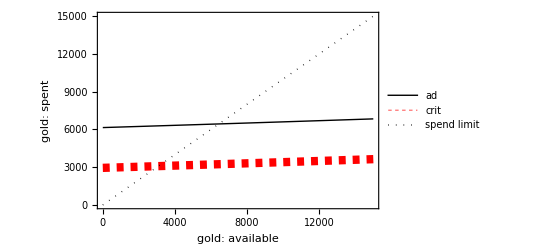

-(4 x+y)^2+(3 x+3 y)^2

5-x^2-7 y^2

(50+x/36) (1+y/5000)

{{0,1/180000},{1/180000,0}}

False

True

True

{{-1,1},{1,1}}

0

10000

-Graphics3D-

√2

√((50+x/36)^2/25000000+(1+y[x]/5000)^2/1296)

(9 (50+x/36))/(1250 (1+y[x]/5000))

1/2 ((50+x/36)/5000+1/36 (1+y[x]/5000))

{1/36 (1+fcrit[u]/5000),(50+fad[u]/36)/5000}

{{Function[{u},-(600 (3 ⅇ^(1/18)-14 ⅇ^(u/180000)))/ⅇ^(1/18)],Function[{u},-(200 (25 ⅇ^(1/18)-42 ⅇ^(u/180000)))/ⅇ^(1/18)]}}

6146.06

2946.06

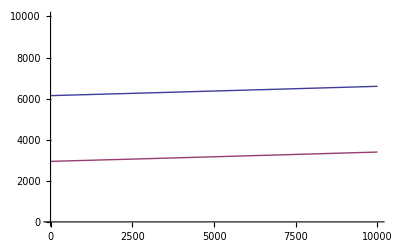

{{100.,3.08463×10^-7},{200.,0.0000156002},{300.,5.95058×10^-7},{400.,8.00896×10^-7},{500.,1.70937×10^-6},{600.,2.21201×10^-6},{700.,2.16881×10^-6},{800.,1.77945×10^-6},{900.,1.27609×10^-6},{1000.,8.18904×10^-7},{1100.,4.99215×10^-7},{1200.,2.37533×10^-6},{1300.,2.93323×10^-6},{1400.,3.67114×10^-6},{1500.,4.74416×10^-6},{1600.,6.47733×10^-6},{1700.,9.66467×10^-6},{1800.,0.000013223},{1900.,0.0000100563},{2000.,0.0000293772},{2100.,0.0000859466},{2200.,0.000260995},{2300.,8.38054×10^-6},{2400.,0.0000960979},{2500.,0.0000667264},{2600.,2.54306×10^-6},{2700.,6.77665×10^-7},{2800.,0.0000276703},{2900.,0.00050378},{3000.,0.000261012},{3100.,0.000444979},{3199.62,0.377847},{3250.,50.0026},{3300.,100.},{3350.,150.},{3400.,200.001},{3450.,250.},{3500.,300.},{3550.,350.},{3600.,400.},{3650.,450.},{3700.,500.},{3750.,550.},{3800.,600.},{3850.,650.},{3900.,700.},{3950.,750.},{4000.,800.},{4050.,850.},{4100.,900.},{4150.,950.},{4200.,1000.},{4250.,1050.},{4300.,1100.},{4350.,1150.},{4400.,1200.},{4450.,1250.},{4500.,1300.},{4550.,1350.},{4600.,1400.},{4650.,1450.},{4700.,1500.},{4750.,1550.},{4800.,1600.},{4850.,1650.},{4900.,1700.},{4950.,1750.},{5000.,1800.},{5050.,1850.},{5100.,1900.},{5150.,1950.},{5200.,2000.},{5250.,2050.},{5300.,2100.},{5350.,2150.},{5400.,2200.},{5450.,2250.},{5500.,2300.},{5550.,2350.},{5600.,2400.},{5650.,2450.},{5700.,2500.},{5750.,2550.},{5800.,2600.},{5850.,2650.},{5900.,2700.},{5950.,2750.},{6000.,2800.},{6050.,2850.},{6100.,2900.},{6150.,2950.},{6200.,3000.},{6250.,3050.},{6300.,3100.},{6350.,3150.},{6400.,3200.},{6450.,3250.},{6500.,3300.},{6550.,3350.},{6600.,3400.}}

-1066.72+0.577697 x

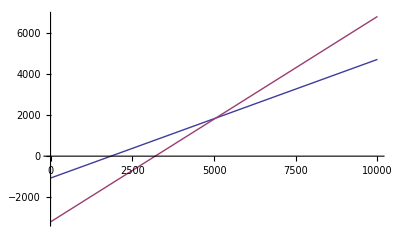

```mathematica
Clear[x,y,z]
ascent[formula_, vars_, {refpoint_,constants_}] := Module[{fs,g,equations,rules,cs},
	fs = Unique/@vars;
	g  = Grad[formula,vars];
	cs        = (#[[1]][refpoint] == #[[2]]&) /@ Thread[{fs,constants}];
	equations = (#[[1]]'[u] == #[[2]]&) /@ Thread[{fs,g}];
	rules = (#[[1]] -> #[[2]][u])& /@ Thread[{vars,fs}];
	(*fs /. DSolve[equations /. rules, fs, u] *)
	Print[cs];
	Print[equations /. rules];
	fs /. DSolve[{equations /. rules, cs}, fs, u] 
	]
ascent[5 - x^2 - 7y^2, {x,y}, {0,{1,1}}]
(*
g = Grad[dps2, {ad,crit}]
{fx,fy} = {x,y} /. First@DSolve[{x'[u] == (g[[1]] /. crit -> y[u]) y'[u] == (g[[2]] /. ad -> x[u]), y[10000]==6600, x[10000]==3400}, {x,y}, u] 
fx[10000]
fy[10000]
fx[0.0]*)
{{fx,fy}} = ascent[dps2, {ad,crit}, {10000,{6600,3400}}]
fx[0.0]
fy[0.0]
Plot[{fx[u],fy[u],u}, {u,0,15000}, PlotLegends -> {ad,crit,"spend limit"}, Frame -> True, FrameLabel -> {"gold: available", "gold: spent"}, 
	PlotStyle -> {Directive[Black,Thick],
				 Directive[Dashed,Red,Thickness[0.015]],
				 Directive[Black,Dotted]}]
g =(3x+3y)^2−(4x+y)^2
g = 5 - x^2 - 7y^2
g = dps2 /. {ad -> x, crit -> y}
hessian[f_,vars_] := D[f,{vars,2}] 
h = hessian[g,{x,y}]
PositiveDefiniteMatrixQ[h]
HermitianMatrixQ[h]
Det[h] ≠ 0
v = Eigenvectors[h]
lo = 0
hi = 10000
Show[Plot3D[g,{x,lo,hi},{y,lo,hi}, 	PlotStyle -> Directive[Pink, Specularity[White, 50], Opacity[0.8]], 
	ExclusionsStyle -> {None, Red}, 
	ClippingStyle -> None, 
	Mesh -> None, 
	Boxed -> False], 
	ParametricPlot3D[With[{xy=t v[[1]]}, {xy⟦1⟧,xy⟦2⟧,g /. {x -> xy⟦1⟧, y -> xy⟦2⟧}}], {t,lo,hi}, PlotStyle -> Directive[Blue,Thick]],
	ParametricPlot3D[With[{xy=t v[[2]]}, {xy⟦1⟧,xy⟦2⟧,g /. {x -> xy⟦1⟧, y -> xy⟦2⟧}}], {t,lo,hi}, PlotStyle -> Directive[Red,Thick]]]
magn[Grad[x y,{x,y}]]  /. {x -> 1, y -> 1}
Clear[f,u,ad,crit,x,y]
slope = magn[Grad[dps2,{ad,crit}]]/. {ad -> x, crit -> y[x]}
slope2 = With[{g=Grad[dps2,{ad,crit}]/. {ad -> x, crit -> y[x]}}, g[[2]]/g[[1]]]
slope3 = With[{g=Grad[dps2,{ad,crit}]/. {ad -> x, crit -> y[x]}}, Total[g]/Length[g]]
slope4 = Grad[dps2,{ad,crit}] /. {ad -> fad[u], crit -> fcrit[u]}
{{ffad,ffcrit}} = {fad,fcrit} /. DSolve[{fad'[u] == slope4[[1]], fcrit'[u] == slope4[[2]], fad[10000]==6600, fcrit[10000]==3400}, {fad,fcrit}, u]
ffad[0.0]
ffcrit[0.0]
Plot[{ffad[u],ffcrit[u]}, {u,0,10000}, PlotRange->{0,10000}]

data = Map[{ad,crit} /. FindMaximum[{dps2,{ad ≥ 0, crit ≥ 0, crit ≤ 5000, ad + crit ≤ 100*#}}, {{ad,0},{crit,0}}][[2]]&, Range[1,100]]
fff = Fit[data, {1,x}, x]
Plot[{fff,-5000+√((1800+x)^2)}, {x,0,10000}]
```

{-2 x,-14 y}

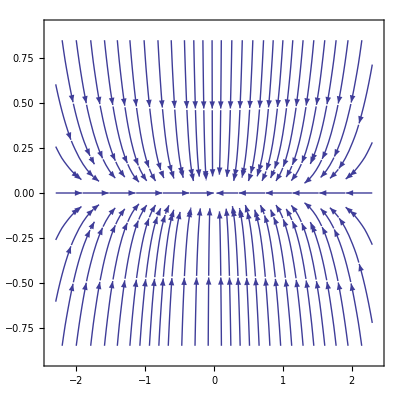

5

{{y[x]→x^7 C[1]}}

{x$77053[0]==1,y$77054[0]==1}

{x$77053'[u]==-2 x$77053[u],y$77054'[u]==-14 y$77054[u]}

{{Function[{u},ⅇ^(-2 u)],Function[{u},ⅇ^(-14 u)]}}

{1.,1.}

{0.0000453999,3.97545×10^-31}

{0.00247875,5.74952×10^-19}

-Graphics3D-

-Graphics3D-

```mathematica
dps3 := (50+(ad/36)) * (1 + (crit/5000)) * (1 + (aspd/3333))

ggg = Grad[dps3,{ad,crit,aspd}];
Clear[ad,crit,aspd,f,x,y]

D[dps3,{{ad,crit,aspd},2}];
f[x_,y_] := 5 - x^2 - 7y^2

dome = Plot3D[f[x,y], {x,-2.3,2.3}, {y,-0.85,0.85}, 
	AxesLabel->{"x","y","z"}, 
	PlotRange -> {0,5},
	PlotStyle -> Directive[Pink, Specularity[White, 50], Opacity[0.8]], 
	ExclusionsStyle -> {None, Red}, 
	ClippingStyle -> None, 
	Mesh -> None, 
	Boxed -> False];

Clear[x,y]
g = Grad[f[x,y],{x,y}]
StreamPlot[g, {x,-2.3,2.3}, {y,-0.85,0.85}]
f[0,0]
DSolve[{y'[x] == (g[[2]]/g[[1]] /. y -> y[x])}, y[x], x]
(*DSolve[{
	(g[[1]]/. y -> y[x]) * y'[x] + 
	(g[[2]]/. y -> y[x])  == 0}, y[x], x]*)
Clear[fx,fy,ffx,ffy,rules]
{{ffx,ffy}} = ascent[f[x,y], {x,y}, {0,{1,1}}]
(*
f[0,0^7]

{rules} = DSolve[{
	fx'[p] == -2fx[p], 
	fy'[p] == -14fy[p]}, {fx,fy}, p] (*5 == 5 - fx[0]^2 - 7fy[0]^2*)

{ffx,ffy} = {fx, fy} /. rules /. {C[1] -> 1.0, C[2] -> 1.0}
*)
{ffx[0.0],ffy[0.0]}
{ffx[5.0],ffy[5.0]}
{ffx[3.0],ffy[3.0]}
(*1, f /. {x -> ffx[u], y -> 1}*)
(*Plot[y /. Solve[x^2+7y^2==5,y][[2]], {x,-3,3}]*)

Show[dome,ParametricPlot3D[{ffx[u],ffy[u],f[ffx[u],ffy[u]]}, {u,-3,3}, PlotRange -> {-3,10}]]
Show[dome,ParametricPlot3D[{x,(x^7)+0,f[x,x^7+0]}, {x,-3,3}, PlotRange -> {-3,10}]]
(*ParametricPlot[{ffx[u], ffy[u]}, {u,-3,3}]*)
```

```mathematica
VectorPlot3D[ggg, {ad,0,10000}, {crit,0,10000}, {aspd,0,10000}, VectorPoints -> Coarse, AxesLabel -> {ad,crit,aspd}]
FindMaximum[{dps3,{ad ≥ 0, crit ≥ 0, aspd ≥ 0, crit ≤ 5000, aspd + ad + crit ≤ 10000}}, {ad,crit,aspd}, MaxIterations -> 20000]
```

-Graphics3D-

$Aborted

```mathematica
Clear[g,fx,fy]
dps3 := (50+(ad/36)) * (1 + (crit/5000)) * (1 + (aspd/3333))
Grad[dps3, {ad,crit,aspd}]
(*gr = Grad[dps2,{ad,crit,aspd}]
gr[[1]] /. {aspd -> 3378.0, crit -> 1711}

fx[p_] := (gr[[1]] /. crit -> y[p])
fy[p_] := (gr[[2]] /. ad -> x[p])

xxx = {x[p],y[p]} /. DSolve[{
	x'[p] == fx[p] y'[p] == fy[p],
	x[10000]==6600,
	y[10000]==3400}, {x[p],y[p]}, p]

xxx /. p -> 10000
N[xxx /. p -> 9000]
N[xxx /. p -> 8000]
N[xxx /. p -> 0]

*)
Clear[t,fx,fy,fz,y,fp,fq,x,y,z,g]
(*
fq[x_,y_,z_] := ((x*2)+(y*4)+(z*3))/8/2
Show[Map[Plot3D[fq[x,y,#]*10, {x,0,60}, {y,0,60}]&, Range[0,1]]]
fq[60,60,60.0]
fq[0,180,0]
FindMaximum[{fq[x,y,z], {x >0, y > 0, z > 0, x+y+z == 180}}, {x,y,z}, MaxIterations -> 20000]
g = Grad[fq[x,y,z], {x,y,z}]
*)
g = Grad[dps3 /. {ad -> x, crit -> y, aspd -> z}, {x,y,z}]
{xxx} = {y[x],z[x]} /. DSolve[{
	y'[x] == (g[[1]] /. y -> y[x]) / g[[2]], 
	z'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[3]] /. y -> y[x]),
	y[4911]==1711,
	z[4911]==3378}, {y[x],z[x]}, x]

hmm[arg_] := {x,xxx[[1]],xxx[[2]]} /. x -> arg
hmm[4911]
hmm[3200]
hmm[0]

Clear[wtf,h,reduction,gAD]

reduction = x /. Solve[{Max[0,xxx[[1]]] + Max[0,xxx[[2]]] + Max[0,x] == h, h ≥ 0}, x, Method ->  Reduce]
(*
gAD[gld_/; gld ≤ 1533] := gld
gAD[gld_/; gld ≤ 4867] := (1533+gld)/2 
gAD[gld_] := (4733+gld)/3*)

gAD[gld_] := Piecewise[{
	{gld, gld ≤ 1533},
	{(1533+gld)/2, gld ≤ 4867}},
	(4733+gld)/3]
gAD[4867]
gCrit[h_] := Max[0,xxx[[1]] /. x -> gAD[h]]
gAspd[h_] := Max[0,xxx[[2]] /. x -> gAD[h]]

gAD[0.0] 
gAD[0]
uhh[u_] := {gAD[u],gCrit[u],gAspd[u]}
uhh[1867.0]
uhh[0.0]
uhh[4867]
uhh[4867]
N[dps3 /. {ad -> 3200, crit -> 0, aspd -> 1667}]
N[dps3 /. {ad -> 3200+500, crit -> 500, aspd -> 1667+500}]
N[dps3 /. {ad -> 3200+1500, crit -> 0, aspd -> 1667}]
N[dps3 /. {ad -> 3200+750, crit -> 750, aspd -> 1667}]
N[dps3 /. {ad -> 3200, crit -> 750, aspd -> 1667+750}]
```

{1/36 (1+aspd/3333) (1+crit/5000),((50+ad/36) (1+aspd/3333))/5000,((50+ad/36) (1+crit/5000))/3333}

{1/36 (1+y/5000) (1+z/3333),((50+x/36) (1+z/3333))/5000,((50+x/36) (1+y/5000))/3333}

{{-3200+x,-1533+x}}

{4911,1711,3378}

{3200,0,1667}

{0,-3200,-1533}

{ConditionalExpression[h,0<h<1533],ConditionalExpression[(1533+h)/2,1533<h<4867],ConditionalExpression[(4733+h)/3,h>4867]}

3200

0.

0

{1700.,0,167.}

{0.,0,0}

{3200,0,1667}

{3200,0,1667}

208.354

277.319

270.86

275.548

275.548

1000.

1

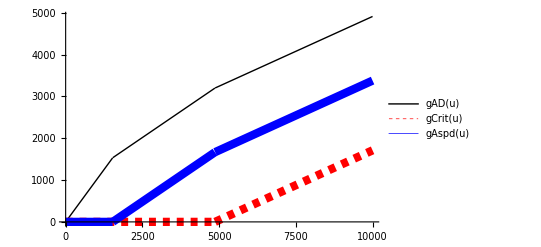

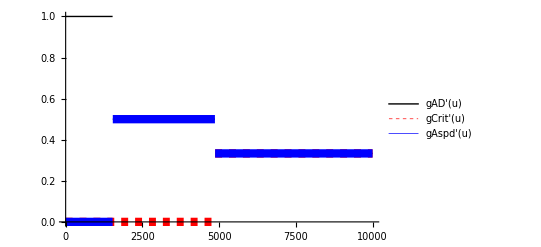

{4911,1711,3378}

-Graphics3D-

{208.354,{ad→3199.81,crit→0.373476,aspd→1666.81}}

{3200,0,1667}

{77.7778,{ad→1000.,crit→0.0000382154,aspd→0.00030284}}

{1000,0,0}

{106.01,{ad→1766.5,crit→0.0000343718,aspd→233.5}}

{1766.5,0,233.5}

```mathematica
gAD[1000.0]
gAD'[1000.0]
Plot[{gAD[u],gCrit[u],gAspd[u]}, {u,0,10000}, PlotLegends -> "Expressions", 
	PlotStyle -> {Directive[Black,Thick],
				 Directive[Dashed,Red,Thickness[0.015]],
				 Directive[Blue,Thickness[0.015],Dashing["Large"]]}]
Plot[{gAD'[u],gCrit'[u],gAspd'[u]}, {u,0,10000}, PlotLegends -> "Expressions", PlotStyle->{Directive[Black,Thick],
				 Directive[Dashed,Red,Thickness[0.015]],
				 Directive[Blue,Thickness[0.015],Dashing["Large"]]}]
uhh[10000]
Show[VectorPlot3D[g, {x,0,10000}, {y,0,10000}, {z,0,10000}, VectorPoints -> Coarse, AxesLabel -> {ad,crit,aspd}],
	ParametricPlot3D[{gAD[u],gCrit[u],gAspd[u]},{u,0,30000}, PlotStyle -> Directive[Red,Thick]]]
(*DSolve[{x'[p] == (g[[1]] /. y -> y[p]) y'[p] == (g[[2]] /. x -> x[p])}, {x[p],y[p]}, p]; *)
(*DSolve[{fx'[p] == 2, fy'[p] == 2}, {fx[p],fy[p]}, p]
DSolve[{fy'[x] == x/16}, {fy[x]}, x]*)
FindMaximum[{dps3,{ad ≥ 0, crit ≥ 0, aspd ≥ 0, crit ≤ 5000, aspd + ad + crit ≤ 4867}}, {ad,crit,aspd}, MaxIterations -> 20000]
uhh[4867]
FindMaximum[{dps3,{ad ≥ 0, crit ≥ 0, aspd ≥ 0, crit ≤ 5000, aspd + ad + crit ≤ 1000}}, {ad,crit,aspd}, MaxIterations -> 20000]
uhh[1000]
FindMaximum[{dps3,{ad ≥ 0, crit ≥ 0, aspd ≥ 0, crit ≤ 5000, aspd + ad + crit ≤ 2000}}, {ad,crit,aspd}, MaxIterations -> 20000]
uhh[2000.0]
```

```mathematica
"
```

1532.88

func | dps | gold distribution | sum | multipliers
old | 92.5833 | ad→1533.
crit→0.
aspd→0. | 1533 | 92.5833
1.
1.
new | 92.5833 | ad→1532.88
crit→0.
aspd→0.12 | 1533. | 92.58
1.
1.00004

func | dps | gold distribution | sum | multipliers
old | 213.946 | ad→3244.33
crit→44.3333
aspd→1711.33 | 5000 | 140.12
1.00887
1.51345
new | 188.885 | ad→1532.88
crit→0.
aspd→3467.12 | 5000. | 92.58
1.
2.04024

func | dps | gold distribution | sum | multipliers
old | 980.08 | ad→6577.67
crit→3377.67
aspd→5044.67 | 15000 | 232.713
1.67553
2.51355
new | 466.653 | ad→1532.88
crit→0.
aspd→13467.1 | 15000. | 92.58
1.
5.04054

{820.768,{232.713,1,3.52695}}

{980.081,{232.713,1.67553,2.51355}}

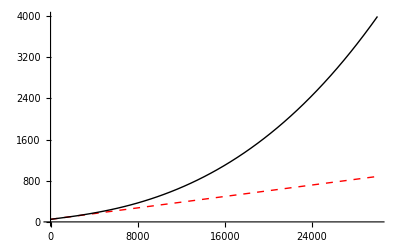

```mathematica
old[u_] := {ad -> gAD[u], crit -> gCrit[u], aspd -> gAspd[u]}

dps3 := (50+(ad/36)) * (1 + (crit/5000)) * (1 + (aspd/3333))
d4 := {50+(ad/36), 1 + (crit/5000), 1 + (aspd/3333)}

threshold = (92.58 - 50) * 36
new[u_] := Piecewise[{
	{{ad -> u, crit -> 0, aspd -> 0}, u ≤ threshold},
	{{ad -> threshold, crit -> 0, aspd -> u-threshold}, True}
	}]

tab[u_] := {{"func", "dps", "gold distribution", "sum", "multipliers"},
			{"old",N[dps3]/. old[u], N@old[u], {ad+crit+aspd}/. old[u], N@(d4 /. old[u])} , 
			{"new", N[dps3]/. new[u], N@new[u], {ad+crit+aspd}/. new[u], N@(d4 /. new[u]) }}
tab[1533] // TableForm
tab[5000] // TableForm
tab[15000] // TableForm
{dps3,d4} /. {ad -> 6577.67, crit -> 0, aspd -> 5044.67+3377.67}
{dps3,d4} /. {ad -> 6577.67, crit -> 3377.67, aspd -> 5044.67}
Plot[{dps3 /. new[u], dps3 /. old[u]}, {u,0,30000}, PlotStyle -> {Directive[Dashed,Red,Thick], Directive[Black,Thick]}]
```